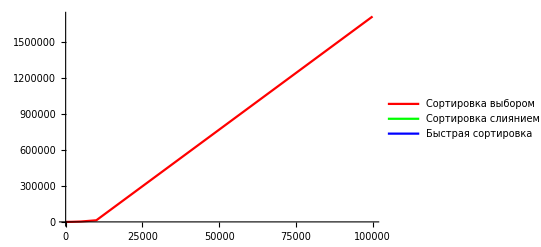

```mathematica
selectSort = ListLinePlot[{{100, 1}, {500, 31}, {1000, 122}, {2000, 484}, {5000, 3023}, {10000, 13476}, {100000, 1715218}}, ColorFunction->Function[{}, Red], PlotLegends->LineLegend[{Red,Green,Blue},{"Сортировка выбором","Сортировка слиянием","Быстрая сортировка"}], PlotRange->All]
```

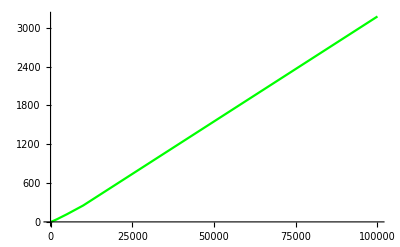

```mathematica
mergeSort = ListLinePlot[{{100, 1}, {500, 8}, {1000, 19}, {2000, 42}, {5000, 118}, {10000, 254}, {100000, 3175}}, ColorFunction->Function[{}, Green],PlotRange->All]
```

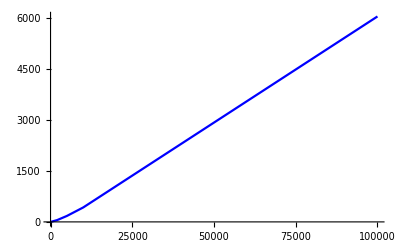

```mathematica
quickSort = ListLinePlot[{{100, 1}, {500, 11}, {1000, 26}, {2000, 52}, {5000, 175}, {10000, 425}, {100000, 6043}}, ColorFunction->Function[{}, Blue], PlotRange->All]
```

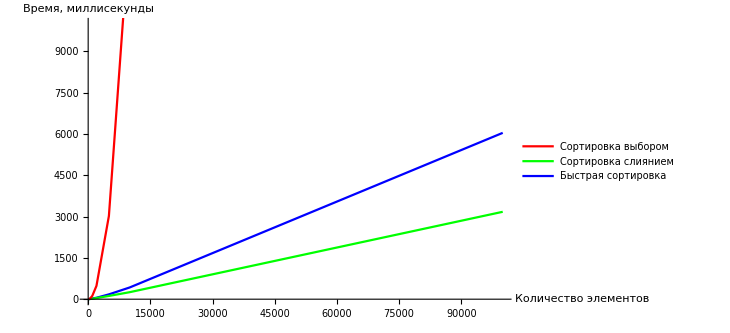

```mathematica
Show[quickSort, mergeSort, selectSort, PlotRange->{0, 10000}, AxesLabel->{"Количество элементов", "Время, миллисекунды"}]
```